# Gubser semi-analytic solution

## Constants

```mathematica
Clear[ℏc,ηOverS,α,c,sols,ρ,T]
```

```mathematica
ℏc=(197.326980/1000); 
ηOverS=0.2;
α=3 π^2/90(2(Nc^2-1)+7/2 Nc Nf)/.{Nc->3,Nf->2.5};
c=5;
```

## Differential equations

```mathematica
sols=NDSolve[{
(T hat'[ρ])/(T hat[ρ])+2/3 Tanh[ρ]==1/3 π bar ηη[ρ]Tanh[ρ],
c/(T hat[ρ])ηOverS(π bar ηη'[ρ]+4/3(π bar ηη[ρ])^2 Tanh[ρ])+π bar ηη[ρ]==4/3 ηOverS/(T hat[ρ])Tanh[ρ],
T hat[0]==3.6,
π bar ηη[0]==0},
{T hat,π bar ηη},
{ρ,-12,12}
];
ρ[τ_,r_]:=ArcSinh[-(1-τ^2+r^2)/(2τ)];
Plot3D[
{ (T hat[ρ[τ,r]])/τ ℏc /.sols,0.100},
{τ,-1, 20},
{r,0.0, 20},
AxesLabel->Automatic,
PlotPoints->100
]
```

-Graphics3D-

```mathematica
sols=NDSolve[{
(T hat'[t])/(T hat[t])+2/3 Tanh[t]==4/9 ηOverS/(T hat[t])Tanh[t]^2,
T hat[0]==(1.2(1.00))/ℏc},
T hat,
{t,-12,12}
];
ρ[τ_,r_]:=ArcSinh[-(1-τ^2+r^2)/(2τ)];
Plot3D[
{ (T hat[ρ[τ,r]])/τ ℏc /.sols,0.130},
{τ,-1, 20},
{r,0.0, 20},
AxesLabel->Automatic,
PlotPoints->100
]
```

-Graphics3D-

```mathematica
sols=NDSolve[{
(T hat'[t])/(T hat[t])+2/3 Tanh[t]==0,
T hat[0]==3.6},
T hat,
{t,-12,12}
];
ρ[τ_,r_]:=ArcSinh[-(1-τ^2+r^2)/(2τ)];
Plot3D[
{ (T hat[ρ[τ,r]])/τ ℏc /.sols,0.5},
{τ,-1, 20},
{r,0.0, 20},
AxesLabel->Automatic,
PlotPoints->100
]
```

-Graphics3D-

## Change of coordinates of solutions

```mathematica
ρ[τ_,r_]:=ArcSinh[-(1-τ^2+r^2)/(2τ)];
T[τ_,r_]:=ℏc((T hat[ρ[τ,r]]/.sols)/τ)[[1]];
T[τ_,x_,y_]:= T[τ,√(x^2+y^2)];
u r[τ_,r_]:=Sinh[ArcTanh[(2τ r)/(1+τ^2+r^2)]];
u x[τ_,x_,y_]:=Piecewise[{{x/(√(x^2+y^2))Sinh[ArcTanh[(2τ √(x^2+y^2))/(1+τ^2+x^2+y^2)]],√(x^2+y^2)≠0},{0.0,√(x^2+y^2)==0}}];
u y[τ_,x_,y_]:=Piecewise[{{y/(√(x^2+y^2))Sinh[ArcTanh[(2τ √(x^2+y^2))/(1+τ^2+x^2+y^2)]],√(x^2+y^2)≠0},{0.0,√(x^2+y^2)==0}}];
π hat ηη[τ_,r_]:=4/3 α ℏc((T hat[ρ[τ,r]]/.sols)[[1]])^4(π bar ηη[ρ[τ,r]]/.sols)[[1]]; 
π ηη[τ_,x_,y_]:=1/τ^6 π hat ηη[τ,√(x^2+y^2)];
π xx[τ_,x_,y_]:=-1/2 1/τ^4(1+Piecewise[{{(x/(√(x^2+y^2)))^2 Sinh[ArcTanh[(2τ √(x^2+y^2))/(1+τ^2+x^2+y^2)]]^2,x^2+y^2≠0},{0.0,x^2+y^2==0}}])π hat ηη[τ,√(x^2+y^2)];
π yy[τ_,x_,y_]:=-1/2 1/τ^4(1+Piecewise[{{(y/(√(x^2+y^2)))^2 Sinh[ArcTanh[(2τ √(x^2+y^2))/(1+τ^2+x^2+y^2)]]^2,x^2+y^2≠0},{0.0,x^2+y^2==0}}])π hat ηη[τ,√(x^2+y^2)];
π xy[τ_,x_,y_]:=Piecewise[{{-1/2 1/τ^4(x y)/(x^2+y^2)Sinh[ArcTanh[(2τ √(x^2+y^2))/(1+τ^2+x^2+y^2)]]^2 π hat ηη[τ,√(x^2+y^2)],x^2+y^2≠0},{0.0,x^2+y^2==0}}];
```

## Plots

### Plot drawing

```mathematica
(* τ's that will be plotted *)
times={1.2,2,3};

plotGrid=GraphicsGrid[
{
{
Plot[Evaluate@Table[T[τ,x,y]/.{τ->times[[i]],y->0},{i,1,Length@times}],{x,-6,6},
PlotRange->{{-6,6},{0.04,0.25}},
Frame->True,AspectRatio->1,GridLines->Automatic,
FrameLabel->{"x [fm]","T [GeV]"},PlotTheme->"Monochrome",PlotStyle->Gray,
Axes->False,PlotLabels->Placed[Table[StringJoin[{"τ=",ToString[times[[i]]]," fm"}],{i,1,Length@times}],Table[{Scaled[0.5],Above},{i,1,Length@times}]]],
Plot[Evaluate@Table[u x[τ,x,y]/.{τ->times[[i]],y->0},{i,1,Length@times}],{x,-6,6},
PlotRange->{{-6,6},{-3,3}},
Frame->True,AspectRatio->1,GridLines->Automatic,
FrameLabel->{"x [fm]","u^x"},PlotTheme->"Monochrome",PlotStyle->Gray,
Axes->False]
},
{
Plot[Evaluate@Table[(τ^2 π ηη[τ,x,y])/.{τ->times[[i]],y->0},{i,1,Length@times}],{x,-6,6},
PlotRange->{{-6,6},{0,0.2}},
Frame->True,AspectRatio->1,GridLines->Automatic,
FrameLabel->{"x [fm]","τ^2π^ηη [GeV/fm^3]"},PlotTheme->"Monochrome",PlotStyle->Gray,
Axes->False],
Plot[Evaluate@Table[π yy[τ,x,y]/.{τ->times[[i]],y->0},{i,1,Length@times}],{x,-6,6},
PlotRange->{{-6,6},{0,-0.12}},
Frame->True,AspectRatio->1,GridLines->Automatic,
FrameLabel->{"x [fm]","π^yy [GeV/fm^3]"},PlotTheme->"Monochrome",PlotStyle->Gray,
Axes->False],

Plot[Evaluate@Table[π xy[τ,x,y]/.{τ->times[[i]],y->x},{i,1,Length@times}],{x,-6,6},
PlotRange->{{-6,6},{0.02,-0.08}},
Frame->True,AspectRatio->1,GridLines->Automatic,
FrameLabel->{"x [fm]","π^xy [GeV/fm^3]"},PlotTheme->"Monochrome",PlotStyle->Gray,
Axes->False]
}
},ImageSize->128*6];
```

### Display plots

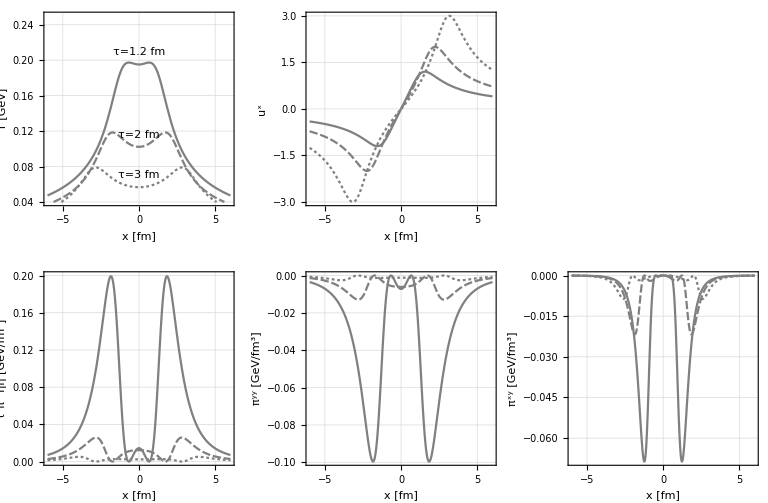

```mathematica
plotGrid
```

## Output table

### Modules to write output files

```mathematica
(* Table with columns "x [fm], y [fm], T [GeV], u^x, u^y, π^xx [GeV/fm^3], π^yy [GeV/fm^3], π^xy [GeV/fm^3], τ^2π^ηη [GeV/fm^3]" as a function of time τ *)
```

```mathematica
formatted InitialProfile Table[τ_:1,gridMax_:5,gridStep_:0.05,path_:NotebookDirectory[]]:=
Module[
{xMax=Abs@gridMax,
xMin=-Abs@gridMax,
yMax=Abs@gridMax,
yMin=-Abs@gridMax,
Δx=Abs@gridStep,
Δy=Abs@gridStep},
outputTable=ArrayFlatten[
Table[{
DecimalForm@N[x,7],
DecimalForm@N[y,7],
DecimalForm@N[T[Τ,x,y],7],
DecimalForm@N[u x[Τ,x,y],7],
DecimalForm@N[u y[Τ,x,y],7],
DecimalForm@N[π xx[Τ,x,y],7],
DecimalForm@N[π yy[Τ,x,y],7],
DecimalForm@N[π xy[Τ,x,y],7],
DecimalForm@N[(Τ^2 π ηη[Τ,x,y]),7]
}/.{Τ->τ},
{x,xMin,xMax,Δx},{y,yMin,yMax,Δy}],1];
format[x_]:=ToString@NumberForm[x,{7,6},NumberFormat->(StringJoin[{#1,""}/. "":>""/;#2==""]&)];
formattedOutput=Map[format,outputTable,{2}];
filename="Initial_Profile_tau="<>ToString[τ]<>"fm.dat";
completePath=FileNameJoin[{path,filename}];
Export[completePath,formattedOutput,"Table","FieldSeparators"->"     "];
];
formatted yeq0 Table[τ_:1,gridMax_:5,gridStep_:0.05,path_:NotebookDirectory[]]:=
Module[
{xMax=Abs@gridMax,
xMin=-Abs@gridMax,
Δx=Abs@gridStep},
outputTable=ArrayFlatten[
Table[{
DecimalForm@N[x,7],
DecimalForm@N[y,7],
DecimalForm@N[T[Τ,x,y],7],
DecimalForm@N[u x[Τ,x,y],7],
DecimalForm@N[u y[Τ,x,y],7],
DecimalForm@N[π xx[Τ,x,y],7],
DecimalForm@N[π yy[Τ,x,y],7],
DecimalForm@N[π xy[Τ,x,y],7],
DecimalForm@N[(Τ^2 π ηη[Τ,x,y]),7]
}/.{Τ->τ,y->0},
{x,xMin,xMax,Δx}],0];
format[x_]:=ToString@NumberForm[x,{7,6},NumberFormat->(StringJoin[{#1,""}/. "":>""/;#2==""]&)];
formattedOutput=Map[format,outputTable,{2}];
filename="y=0_tau="<>ToString[τ]<>"_SemiAnalytic.dat";
completePath=FileNameJoin[{path,filename}];
Export[completePath,formattedOutput,"Table","FieldSeparators"->"     "];
];
formatted yeqx Table[τ_:1,gridMax_:5,gridStep_:0.05,path_:NotebookDirectory[]]:=
Module[
{xMax=Abs@gridMax,
xMin=-Abs@gridMax,
Δx=Abs@gridStep},
outputTable=ArrayFlatten[
Table[{
DecimalForm@N[x,7],
DecimalForm@N[y,7],
DecimalForm@N[T[Τ,x,y],7],
DecimalForm@N[u x[Τ,x,y],7],
DecimalForm@N[u y[Τ,x,y],7],
DecimalForm@N[π xx[Τ,x,y],7],
DecimalForm@N[π yy[Τ,x,y],7],
DecimalForm@N[π xy[Τ,x,y],7],
DecimalForm@N[(Τ^2 π ηη[Τ,x,y]),7]
}/.{Τ->τ,y->x},
{x,xMin,xMax,Δx}],0];
format[x_]:=ToString@NumberForm[x,{7,6},NumberFormat->(StringJoin[{#1,""}/. "":>""/;#2==""]&)];
formattedOutput=Map[format,outputTable,{2}];
filename="y=x_tau="<>ToString[τ]<>"_SemiAnalytic.dat";
completePath=FileNameJoin[{path,filename}];
Export[completePath,formattedOutput,"Table","FieldSeparators"->"     "];
]
```

### Call module

```mathematica
formatted InitialProfile Table[1,6,0.05]
```

```mathematica
formatted yeq0 Table[1,5,0.05]
```

```mathematica
formatted yeqx Table[2.3,5,0.05]
```